```mathematica
Clear["Global`*"]
```

1.  Normal distribution. Apply the maximum likelihood method to the normal distribution with μ = 0.

What did I do here? I ginned up a list of outcomes using the normal distribution with the mean required by the problem description and a small standard deviation. Then I asked Mathematica to create a distribution based on the characteristics of the list members and the ParameterEstimator using the “MaximumLikelihood” method. I can view the distribution created and judge its fidelity to the original.

```mathematica
data=RandomVariate[NormalDistribution[0,0.001],10000];
EstimatedDistribution[data,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[5.67086×10^-6,0.00100286]

I notice that each time I re-run the above command the output changes slightly.

The ParameterEstimator procedure has a half dozen search methods, including

```mathematica
EstimatedDistribution[data,NormalDistribution[n,p],ParameterEstimator->{"MethodOfMoments"}]
```

NormalDistribution[5.67086×10^-6,0.00100286]

```mathematica
EstimatedDistribution[data,NormalDistribution[n,p],ParameterEstimator->{"MethodOfCumulants"}]
```

NormalDistribution[5.67086×10^-6,0.00100286]

I could plot the pdfs of the three manufactured distributions but there would be nothing to distinguish one from another.

3.  Poisson distribution. Derive the maximum likelihood estimator for μ. Apply it to the sample (10, 25, 26, 17, 10, 4), giving numbers of minutes with 0 - 10, 11 - 20, 21 - 30, 31 - 40, 41 - 50, more than 50 fliers per minute, respectively, checking in at some airport check-in.

```mathematica
Clear["Global`*"]
```

I was able to hit the right buttons on this one, I think.

```mathematica
data={10,25,26,17,10,4}
```

{10,25,26,17,10,4}

```mathematica
FindDistributionParameters[data,PoissonDistribution[μ],ParameterEstimator->{"MaximumLikelihood",Method->"NMaximize"}]
```

{μ→15.3333}

The answer above matches the answer in the text.

5.  Binomial distribution. Derive a maximum likelihood estimate for p.

```mathematica
Clear["Global`*"]
```

```mathematica
data=RandomVariate[BinomialDistribution[10,0.4],1000];
dink=EstimatedDistribution[data,BinomialDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

BinomialDistribution[9,0.453778]

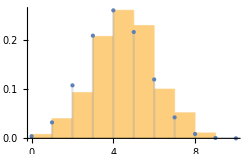

```mathematica
Show[Histogram[data,{0,10,1},"PDF"],DiscretePlot[PDF[dink,x],{x,0,11},PlotStyle->PointSize[Medium]],ImageSize->250]
```

If the maximum likelihood is at least nominal, as here, I would have to consider it as reasonably likely to represent the goal of the exercise.

```mathematica
data1=RandomVariate[BinomialDistribution[10,0.4],10000];
dink1=EstimatedDistribution[data1,BinomialDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

BinomialDistribution[10,0.40283]

```mathematica
data2=RandomVariate[BinomialDistribution[10,0.4],30000];
dink2=EstimatedDistribution[data2,BinomialDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

BinomialDistribution[10,0.400487]

Above I see the natural tendency for the maximum likelihood to go down as the sample size increases.

6.  Extend problem 5 as follows. Suppose that m times n trials were made and in the first n trials A happened k_1 times, in the second n trials A happened k_2 times, . . . , in the mth n trials A happened k_m times. Find a maximum likelihood estimate of p based on this information.

7.  Suppose that in problem 6 we made 3 times 4 trials and A happened 2, 3, 2 times, respectively. Estimate p.

```mathematica
Clear["Global`*"]
```

```mathematica
data7=RandomVariate[BinomialDistribution[12,7/12],100000];
```

```mathematica
dink71=EstimatedDistribution[data7,BinomialDistribution[n,p],ParameterEstimator->{"MethodOfMoments"}]
```

BinomialDistribution[12.0097,0.582034]

```mathematica
dink72=EstimatedDistribution[data7,BinomialDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

BinomialDistribution[12,0.582506]

```mathematica
dink73=EstimatedDistribution[data7,BinomialDistribution[n,p],ParameterEstimator->{"MethodOfCentralMoments"}]
```

BinomialDistribution[12.0097,0.582034]

```mathematica
dink74=EstimatedDistribution[data7,BinomialDistribution[n,p],ParameterEstimator->{"MethodOfCumulants"}]
```

BinomialDistribution[12.0097,0.582034]

```mathematica
dink75=EstimatedDistribution[data7,BinomialDistribution[n,p],ParameterEstimator->{"MethodOfFactorialMoments"}]
```

BinomialDistribution[12.0097,0.582034]

```mathematica
N[7/12]
```

0.583333

A couple of comments. I notice that RandomVariate will accept a rational fraction as standard deviation. As for the given information, I don’t think the number of trials matters, I believe that only the raw ratio is important here. After many run-throughs of testing, I see the following: Concerning the RandomVariate, the sample size, the last number, can’t smooth out the sample if the first number, trials, has small precision. This makes sense, though with problem 7 it is a fly in the ointment. As for the dinks, the MaximumLikelihood always differs from the other methods, though not always on the high side of the theoretical ratio decimal value. The other four methods, in my experience, always come up with exactly the same answer on this problem.

8.  Geometric distribution. Let X = Number of independent trials until an event A occurs. Show that X has a geometric distribution, defined by the probability function f[x] = pq^(x-1), x = 1, 2, . . . , where p is the probability of A in a single trial and q = 1 - p. Find the maximum likelihood estimate of p corresponding to a sample x_1 , x_2 , . . . , x_n of observed values of X.

9.  In problem 8, show that f(1) + f(2) + . . . + = 1 (as it should be). Calculate independently of problem 8 the maximum likelihood of p in problem 8 corresponding to a single observed value of X.

```mathematica
Clear["Global`*"]
```

```mathematica
inr=PDF[GeometricDistribution[p],k]
```

Piecewise[{{(1-p)^k p, k≥0}, {0, True}}]

```mathematica
tri=Sum[inr, {k,0,10}]
```

p+(1-p) p+(1-p)^2 p+(1-p)^3 p+(1-p)^4 p+(1-p)^5 p+(1-p)^6 p+(1-p)^7 p+(1-p)^8 p+(1-p)^9 p+(1-p)^10 p

```mathematica
tri/.p->0.8
```

1.

The pdf shown above is equivalent to the one described in problem 8.

```mathematica
data9=RandomVariate[GeometricDistribution[0.1],1]
```

{3}

```mathematica
dib=EstimatedDistribution[data9,GeometricDistribution[n],ParameterEstimator->{"MaximumLikelihood"}]
```

GeometricDistribution[0.25]

Observations on this problem. RandomVariate and the GeometricDistribution will not produce a non-zero single sample unless the input probability is 0.4 or less. If X is the sample, then the output probability is approximately 1/X, which is the text answer for this problem.

11.  Find the maximum likelihood estimate of θ in the density f[x] = θ ⅇ^(-θ x) if x ≥ 0 and f[x] = 0 if x < 0.

```mathematica
Clear["Global`*"]
```

The following is not the way to define the desired distribution, because Mathematica can’t understand this formatting.

```mathematica
dist=ProbabilityDistribution[Piecewise[{{θ ⅇ^(-θ x),x≥0},{0,x<0}}],{x,0,∞},Assumptions->{θ>0}];

PDF[dist[],x]
```

PDF[ProbabilityDistribution[Piecewise[{{ⅇ^(-x θ) θ, x≥0}, {0, True}}],{x,0,∞},Assumptions→{θ>0}][],x]

As an improvement on the above, the following was tried thanks to an example by Bob Hanlon on https://mathematica.stackexchange.com/questions/72996/custom-distribution

```mathematica
dist2=ProbabilityDistribution[θ ⅇ^(-θ x),{x,0,∞},Assumptions->{θ>0}]
```

ProbabilityDistribution[ⅇ^(-x θ) θ,{x,0,∞},Assumptions→{θ>0}]

For Mathematica to return the pdf in processed form is a good sign.

```mathematica
PDF[dist2,x]
```

Piecewise[{{ⅇ^(-x θ) θ, x>0}, {0, True}}]

```mathematica
dpa=DistributionParameterAssumptions[dist2]
```

{θ>0}

The pdf turns out to be normalized.

```mathematica
Assuming[dpa,Integrate[PDF[dist2,x],{x,0,Infinity}]]
```

1

```mathematica
Assuming[dpa,Mean[dist2]//FullSimplify]
```

1/θ

```mathematica
Assuming[dpa,StandardDeviation[dist2]//Simplify]
```

1/θ

With mean equal to s.d. , I want to try the following.

```mathematica
PDF[dist2,x]==PDF[ExponentialDistribution,x]//Simplify[#,dpa]&
```

PDF[ExponentialDistribution,x]==(Piecewise[{{ⅇ^(-x θ) θ, x>0}, {0, True}}])

The above cell does not prove that dist2 is exponential, but in appearance it is exponential. I can choose θ to be 0.6 just for grins and try out a MaximumLikelihood move.

```mathematica
data11=RandomVariate[ExponentialDistribution[0.6],100000];
```

```mathematica
EstimatedDistribution[data11,ExponentialDistribution[p],ParameterEstimator->{"MaximumLikelihood"}]
```

ExponentialDistribution[0.601181]

This is not what the text answer looks like, that being θ̂ = 1/x^__ .

13.  Compute θ̂ in problem 11 from the sample 1.9, 0.4, 0.7, 0.6, 1.4. Graph the sample distribution function F̂[x] and the distribution function F[x] of the random variable, with θ = θ̂, on the same axes. Do they agree reasonably well? (We consider goodness of fit systematically in section 25.7.)

```mathematica
myemp=EmpiricalDistribution[{1.9,0.4,0.7,0.6,1.4}]
```

DataDistribution[…]

```mathematica
data13={1.9,0.4,0.7,0.6,1.4}
```

{1.9,0.4,0.7,0.6,1.4}

```mathematica
p1=DiscretePlot[CDF [myemp,x],{x,-4,4,.01},PlotStyle->Red,ImageSize->250];
```

```mathematica
sec=EstimatedDistribution[data13,ExponentialDistribution[p],ParameterEstimator->{"MaximumLikelihood"}]
```

ExponentialDistribution[1.]

The above answer agrees (accidentally?) with the text answer.

```mathematica
p2=DiscretePlot[CDF [sec,x],{x,-4,4,.01}];
```

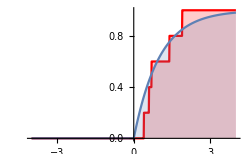

```mathematica
Show[p1,p2]
```

15.  CAS EXPERIMENT. Maximum likelihood estmates. (MLEs). Find experimentally how much MLEs can differ depending on the sample size. Hint. Generate many samples of the same size n, e.g. of the standardized normal distribution, and record x̄ and s^2. Then increase n.

This is indeed an experiment. If the cells were to be run again, all answers would be different. It demonstrates that sample size is limited in influence so long as the mean and standard deviation are expressed coarsely.

```mathematica
Clear["Global`*"]
```

```mathematica
data15a=RandomVariate[NormalDistribution[0.2, 0.01],4];
data15b=RandomVariate[NormalDistribution[0.2, 0.01],12];
data15c=RandomVariate[NormalDistribution[0.2, 0.01],100];
data15d=RandomVariate[NormalDistribution[0.2, 0.01],1000];
data15e=RandomVariate[NormalDistribution[0.2, 0.01],10000];
data15f=RandomVariate[NormalDistribution[0.2, 0.01],100000];
```

```mathematica
d15a=EstimatedDistribution[data15a,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.197877,0.0105572]

```mathematica
d15b=EstimatedDistribution[data15b,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.202904,0.00793746]

```mathematica
d15c=EstimatedDistribution[data15c,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.199636,0.00986493]

```mathematica
d15d=EstimatedDistribution[data15d,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.199854,0.00995169]

```mathematica
d15e=EstimatedDistribution[data15e,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.199871,0.0100522]

```mathematica
d15f=EstimatedDistribution[data15f,NormalDistribution[n,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0.199941,0.00994559]

```mathematica
n1=Abs[0.2-d15a[[1]]];
n2=Abs[0.01-d15a[[2]]];
n3=Abs[0.2-d15b[[1]]];
n4=Abs[0.01-d15b[[2]]];
n5=Abs[0.2-d15c[[1]]];
n6=Abs[0.01-d15c[[2]]];
n7=Abs[0.2-d15d[[1]]];
n8=Abs[0.01-d15d[[2]]];
n9=Abs[0.2-d15e[[1]]];
n10=Abs[0.01-d15e[[2]]];
n11=Abs[0.2-d15f[[1]]];
n12=Abs[0.01-d15f[[2]]];
```

```mathematica
g2=Grid[{{" trial ", "sample"," error mean "," error s.d. "}},Frame->All];
```

```mathematica
g1=Grid[{{"data15a",4,n1,n2},{"data15b",12,n3,n4},{"data15c",100,n5,n6},{"data15d",1000,n7,n8},{"data15e",10000,n9,n10},{"data15f",100000,n11,n12}},Frame->All];
```

```mathematica
Column[{g2,g1}]
```

trial  | sample |  error mean  |  error s.d. 
data15a | 4 | 0.00212348 | 0.000557249
data15b | 12 | 0.00290421 | 0.00206254
data15c | 100 | 0.00036434 | 0.00013507
data15d | 1000 | 0.000146174 | 0.0000483148
data15e | 10000 | 0.000128969 | 0.0000522355
data15f | 100000 | 0.0000593452 | 0.0000544065

In the above Grid it can be seen that the results of the MaximumLikelihood search get closer to the nominal values as the samples get larger.